```mathematica
ClearAll["Global`*"]
```

# Method of finite differences

Bibliography:  Datta.S  - Quantum Transport : from Atom to Transistor

### Objective

```mathematica
-Graphics-;
```

### method

```mathematica
-Graphics-;
```

### matrix equation :

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```

## code

### parâmetros

```mathematica
xmin=-10.;
xmax=10.;
a=.01;
N0Grid=Round[(xmax-xmin)/a]+1;
xvalues=Range[xmin,xmax,a];
```

### Potencial

```mathematica
V1[x_]=1/2.(-10*x^2+x^4);
```

### matriz

```mathematica
Tmtx=-(1/(2 (a)^2)) SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1},{N0Grid,N0Grid}];
Vmtx=DiagonalMatrix[V1/@Range[xmin,xmax,a]];
Hmtx=Tmtx+Vmtx;
```

### diagonalização

lista com {valor próprio, vector próprio}

```mathematica
result=Sort[Transpose@Eigensystem[Hmtx],(#1[[1]]<#2[[1]])&];
```

```mathematica
energias = result[[All,1]];
```

### Plots

```mathematica
result[[All,2]][[1;;4]];
```

```mathematica
xvalues;
```

```mathematica
{#,#^2}&/@xvalues;
```

```mathematica
({xvalues,#}//Transpose)&/@result[[All,2]]//Transpose;
```

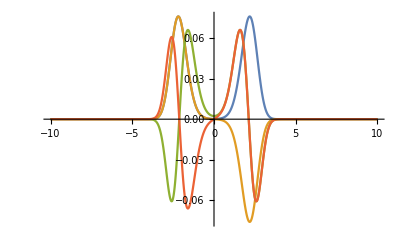

```mathematica
ListPlot[Transpose[{xvalues,#}]&/@result[[All,2]][[1;;4]],Joined->True,PlotRange->All]
```

```mathematica
Manipulate[
Column[
{"energia=" <>ToString(energias)}
```

```mathematica
],
{{i,1},
}
]
]
```